This programme was originally written by Dónal Flanagan as part of a M. Sc. thesis in physics entitled “Surface-enhanced Raman spectroscopy on nano-patterned copper”.

The  work shown here was carried out in the research group of Prof. Dr. Stephanie Reich at the Freie Universität Berlin as part of a collaborative research project in surface enhanced Raman spectroscopy with Atotech Berlin GmBH and  Prof. Eric Anglaret of the Universitê Montpellier II.

The programme is designed for the analysis of CVD graphene but may be easily edited to analyse maps of other materials. 

If you have any questions or problems using this programme please feel free to contact me at:
https://www.linkedin.com/in/donaloflanagain
www.xing.com/profile/Donal_Flanagan3
and I will do my best to reply. 

This programme is for testing the fit parameters and results for a single spectrum.

## Functions Library

#### Importing data and extracting variables/arrays

```mathematica
ClearAll["Global`*"]

extractlocations[filepath_]:=(
filename=FileBaseName[filepath];folderpath=DirectoryName[filepath];dir=DirectoryName[folderpath];Return[filename];Return[folderpath];Return[dir];)

splitfilename[filename_]:=(
split=StringSplit[filename,"_"];mapname=split[[1]];X=ToExpression[split[[2]]];Y=ToExpression[split[[3]]];Return[mapname];Return[Y];Return[X];)
(*
mapname=split[[1]]<>"_"<>split[[2]]<>"_"<>split[[3]];X=ToExpression[split[[4]]];Y=ToExpression[split[[5]]];

mapname=split[[1]];X=ToExpression[split[[2]]];Y=ToExpression[split[[3]]];
*)

importdata[folderpath_,mapname_,X_,Y_]:=(
fullmapdata=Import[folderpath<>mapname<>"_"<>ToString[X]<>"_"<>ToString[Y]<>".txt","TSV"];
Return[fullmapdata];)

Initial parameters;
(* Here we take the imported dataset 'fullmapdata' and divide it into smaller datasets that can be operated on seperately. *)

(* The main background, excluding all peaks. An exponential background will be fit to this *)
extractbackground[fullmapdata_]:=(
backgrounddata=Join[
Select[fullmapdata,1028.<#[[1]]<1230.&],
Select[fullmapdata,1380.<#[[1]]<1480.&],
Select[fullmapdata,1720.<#[[1]]<2380.&],
Select[fullmapdata,2770.<#[[1]]<2835.&],
Select[fullmapdata,2995.<#[[1]]<3180.&],
Select[fullmapdata,3300.<#[[1]]&]];
Return[backgrounddata];
)

(* This is the list of wavenumber ranges in which the peaks lie. It corresponds to {D peak, G peak, 2D peak, Oxide peak}. These values are passed to the 'selectpeakdata' function. *)
peakrangelist={{1150.,1480.},{1450.,1710.},{2300.,2800.}};

(* This is the list of ranges to which we constrain the three peaks around the 2D peak. It corresponds too {{2D},{ddash, 2D},{dddash, strainpeak, 2D}} *)
constraintslist={{2440,2495,2620,2660},{2440,2495,2550,2610,2620,2650}};

(* This is the function that takes the fullmapdata and extracts the regions the peaks are in. xmin and xmax are the values from peakrangelist, dataset is fullmapdata, and g is the data returned and assigned to peakDdata, etc. *)
selectpeakdata[dataset_,xmin_, xmax_]:=(
g=Select[dataset,xmin<#[[1]]<xmax&];
Return[g];)

(* This function takes the peak data sets and returns initial parameters for the fit function. 
Not sure if I need to include this:
Clear[Ainit,winit,xinit,hmax,hmin,hinit]
 *)
initialparameterfunc[dataset_]:=(
hmax=0;
winit=20;
hmin=100000;
For[j=1,j≤Length[dataset],j++,
If [dataset[[j,2]]>hmax,{hmax=dataset[[j,2]],xinit=dataset[[j,1]]},0];
If [dataset[[j,2]]<hmin,{hmin=dataset[[j,2]]},0];];
hinit=hmax-hmin;
Ainit=hinit*Pi*winit;
Return[{Ainit,winit,xinit}];
)

Fit each peak: D, G, 2D and background;

lorentzmodel[area_,w_,pos_,x_]=(2*area/Pi)*(w/(4*(x-pos)^2+(2 w)^2));
gaussmodel[area_,w_,pos_,x_]=area^2 E^(-((x-pos)^2/(2 w^2)));

(* PEAK FUNC WITH INITIAL PARAMETERS *)
lorentzfunc[background_,peakdata_,Ainit_,winit_,xinit_]:=(
model=background[x]+(2*area/Pi)*(w/(4*(x-pos)^2+(2 w)^2));
fit=NonlinearModelFit[peakdata,model,{{area,Ainit},{w,winit},{pos,xinit}},x,MaxIterations->300];
Return[fit];)

(* PEAK FUNC WITH CONSTRAINTS *)
fit2Dfunc2[background_,peakdata_,x1min_,x1max_,x2min_,x2max_]:=(
model=background[x]+area1^2 E^(-((x-pos1)^2/(2 w1^2)))+(2*area2/Pi)*(w2/(4*(x-pos2)^2+(2 w2)^2));
fit=NonlinearModelFit[peakdata,{model,{0<w1<20,x1min<pos1<x1max,10<w2<30,x2min<pos2<x2max}},{area1,w1,pos1,area2,w2,pos2},x,MaxIterations->400];
Return[fit];)

(* Fits a gaussian (D+D'), a lorentzian (strained 2D) and another lorentzian (2D) *)
fit2Dfunc3[background_,peakdata_,x1min_,x1max_,x2min_,x2max_,x3min_,x3max_]:=(
model=background[x]+area1^2 E^(-((x-pos1)^2/(2 w1^2)))+(2*area2/Pi)*(w2/(4*(x-pos2)^2+(2 w2)^2))+(2*area3/Pi)*(w3/(4*(x-pos3)^2+(2 w3)^2));fit=NonlinearModelFit[peakdata,{model,{0<w1<20,x1min<pos1<x1max,0<w2<20,x2min<pos2<x2max,5<w3<30,x3min<pos3<x3max}},{area1,w1,pos1,area2,w2,pos2,area3,w3,pos3},x,MaxIterations->400];
Return[fit];)

Dpeakfittingfunction2[background_,peakdata_]:=(
model=background[x]+(2*area/Pi)*(w/(4*(x-pos)^2+(2 w)^2));
fit=NonlinearModelFit[peakdata,{model,{0<w<30,1180<pos<1380}},{area,w,pos},x,MaxIterations->600];
Return[fit];)

exportfunction[dir_,mapname_,Results_]:=(
resultsdir=CreateDirectory[dir<>"Results//"];Export[resultsdir<>mapname<>".txt",Results,
"TSV"];)

mapplot[mapdata_,min_,max_,label_]:=(
map=ListDensityPlot[
mapdata,DataRange->Automatic,PlotRange->{All,All,{min,max}},PerformanceGoal->"Quality",
ColorFunction->"DarkRainbow",ColorFunctionScaling->True,LabelStyle->(FontSize-> 18),
PlotLegends->BarLegend[{"DarkRainbow",{min,max}},LegendLabel->label,LabelStyle->(FontSize-> 18),LegendMarkerSize->260],FrameLabel-> {{"μm",None},{"μm",None}},Frame-> True];
Return[map];
)

mapplot3D[mapdata_,min_,max_,label_]:=(
map3D=ListPlot3D[
mapdata,DataRange->Automatic,PlotRange->{All,All,{min,max}},PerformanceGoal->"Quality",
ColorFunction->"DarkRainbow",ColorFunctionScaling->True,LabelStyle->(FontSize-> 20),
PlotLegends->BarLegend[{"DarkRainbow",{min,max}},LegendLabel->label,LabelStyle->(FontSize-> 20)],AxesLabel->{"μm","μm",None},ImageSize->{Automatic,500}];
Return[map3D];
)

histdistfunc[dist_,distdata_,alldata_]:=(

Clear[ab,mean,standev,chi,distribution,logdistribution,hist,loghist,shorthist,histogram,loghistogram,shorthistogram];

ab=EstimatedDistribution[distdata,dist[a,b]];

mean=Mean[ab];
standev=StandardDeviation[ab];
chi=PearsonChiSquareTest[distdata,ab];

distribution=Plot[
bin*Length[distdata]*PDF[ab,x],{x,0,50000},PlotRange-> All,PlotStyle->{Thick},Frame->True,PlotRangeClipping-> True];

logdistribution=LogLinearPlot[
bin*Length[distdata]*PDF[ab,x],{x,1,50000},PlotRange-> All,PlotStyle->{Thick},Frame->True,PlotRangeClipping-> True];


shorthist=Histogram[distdata,{bin},
Frame->True, LabelStyle->{Bold,Medium},PlotLabel->Style["Distribution of G peak area values below 45,000 a.u.",17],BaseStyle->{FontFamily-> "Helvetica"},FrameLabel->{"G peak area (a.u.)"},PlotRangeClipping-> True,
ChartLabels->Placed[{{"Mean: "},{mean},{"Standard deviation: "},{standev},{"χ.b2 ="},{chi}},{{0.86,1.1},{0.94,1.1},{0.79,1.04},{0.94,1.04},{0.86,0.98},{0.94,0.98}}]];

hist=Histogram[alldata,{bin},
Frame->True, LabelStyle->{Bold,Medium},PlotLabel->Style["Distribution of G peak area values",17],
BaseStyle->{FontFamily-> "Helvetica"},FrameLabel->{"G peak area (a.u.)"},PlotRangeClipping-> True,
ChartLabels->Placed[{{"Mean: "},{mean},{"Standard deviation: "},{standev},{"χ.b2 ="},{chi}},{{0.86,1.1},{0.94,1.1},{0.79,1.04},{0.94,1.04},{0.86,0.98},{0.94,0.98}}]];

loghist=Histogram[alldata,{bin},ScalingFunctions->{"Log"},
Frame->True, LabelStyle->{Bold,Medium},PlotLabel->Style["Distribution of G peak area values",17],
BaseStyle->{FontFamily-> "Helvetica"},FrameLabel->{"G peak area (Log{a.u.})"},PlotRangeClipping-> True,
ChartLabels->Placed[{{"Mean: "},{mean},{"Standard deviation: "},{standev},{"χ.b2 ="},{chi}},{{0.86,1.1},{0.94,1.1},{0.79,1.04},{0.94,1.04},{0.86,0.98},{0.94,0.98}}]];


shorthistogram=Show[shorthist,distribution,ImageSize-> Large,LabelStyle->(FontSize-> 17)];
histogram=Show[hist,distribution,ImageSize-> Large,LabelStyle->(FontSize-> 17)];
loghistogram=Show[loghist,logdistribution,ImageSize-> Large,LabelStyle->(FontSize-> 17)];

Print["Finished histogram and distribution"];

Return[shorthistogram];
Return[loghistogram];
Return[histogram];
)
```

## Main

#### Import Data

For simplicity we will have the user select one of the files in the map. Then we can extract the filename, foldername and folder directory from this.
Please select the file containing the last spectra/pixel in the map.
i.e. In a 50x70 step map named ‘1LG-Raman’, select ‘1LG-Raman_ 50_ 70.txt.’

```mathematica
polynomialfitfilepath="C:\\Users\\donal\\Desktop\\Map Fitting Programme\\PolynomialFit.m";
filepath=FileNameSetter[Dynamic[filepath]]
```

$CellContext`filepathOpenAll

```mathematica
(* If you know the file path and don't want to look it up every time just skip the previous step and put it in here. *)
filepath="C:\\Users\\donal\\Desktop\\Map Fitting Programme\\Strained test data\\map4 split_cm-1\\map4_21_26.txt"
```

C:\Users\donal\Desktop\Map Fitting Programme\Strained test data\map4 split_cm-1\map4_21_26.txt

#### Execute Fitting Programme

map4_21_26

map4

Check before

General::obspkg: "NumericalMath`PolynomialFit`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Needs::nocont: Context "PolynomialFit`" was not created when Needs was evaluated.

Check after

The background fit is

FittingPolynomial[<>, 6]

The background value at x=250 is

291.904

FittedModel::constr: The property values {"ParameterTableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

fitDParameters=fitD[ParameterTableEntries]

{{5675.9,435.598,13.0301,2.86385×10^-21},{16.1633,1.7546,9.21194,4.18933×10^-14},{1321.34,1.23846,1066.92,3.55484×10^-164}}

fitGParameters=fitG[ParameterTableEntries]

{{18879.6,807.536,23.3793,4.72263×10^-33},{17.6907,1.07063,16.5237,8.98743×10^-25},{1580.74,0.753609,2097.56,1.60319×10^-156}}

FittedModel::constr: The property values {"ANOVATableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

Dfit is

FittedModel[70.6755+(«19»)/(«19»+4 «1»)+«1»«1»«22» «1» (-«18»+x)+0.000619966 (-36.4227+«4») (-2452.28+x)]

fitDO = 0

background[#1]+0 #1&

The background fit to data variance is

7.33726×10^-6

The D peak fit to data variance is

0.0464645

The Dpeakvariance is

0.0464645

fitD=Which[Dpeakvariance==Dbackgroundvariance,fitDO,Dpeakvariance==Dfitvariance,Dfit]

FittedModel[70.6755+(«19»)/(«19»+4 «1»)+«1»«1»«22» «1» (-«18»+x)+0.000619966 (-36.4227+«4») (-2452.28+x)]

Evaluate[fitDvals]=Which[Dpeakvariance==Dbackgroundvariance,Dfitvals,Dpeakvariance==Dfitvariance,fitDOvals]

{5675.9,16.1633,1321.34}

fitD is

FittedModel[70.6755+(«19»)/(«19»+4 «1»)+«1»«1»«22» «1» (-«18»+x)+0.000619966 (-36.4227+«4») (-2452.28+x)]

fitDvals are

{5675.9,16.1633,1321.34}

Gfit is

FittedModel[70.6755+(«19»)/(«18»+4 «1»)+«1»«1»«22» «1» (-«18»+x)+0.000619966 (-36.4227+«4») (-2452.28+x)]

fitGO is

background[#1]+0 #1&

The background fit to data variance is

5.73884×10^-11

The G peak fit to data variance is

0.272271

The Gpeakvariance is

0.272271

fitG=Which[Gpeakvariance==Gbackgroundvariance,fitGO,Gpeakvariance==Gfitvariance,Gfit]

FittedModel[70.6755+(«19»)/(«18»+4 «1»)+«1»«1»«22» «1» (-«18»+x)+0.000619966 (-36.4227+«4») (-2452.28+x)]

Evaluate[fitDvals]=Which[Gpeakvariance==Gbackgroundvariance,GfitOvals,Gpeakvariance==Gfitvariance,Gfitvals]

{18879.6,17.6907,1580.74}

fitG is

FittedModel[70.6755+(«19»)/(«18»+4 «1»)+«1»«1»«22» «1» (-«18»+x)+0.000619966 (-36.4227+«4») (-2452.28+x)]

fitGvals are

{18879.6,17.6907,1580.74}

2Dfitinit is

FittedModel[70.6755+10.9033 ⅇ^(-«21» («1»)^2)+«5»+0.000619966 («1») (-2452.28+x)]

fit2DO is

background[#1]+0 #1&

The background fit to data variance is

4.48956×10^-43

The D peak fit to data variance is

0.159743

The Dpeakvariance is

0.159743

fit2D=Which[2Dpeakvariance==2Dbackgroundvariance,fit2DO,2Dpeakvariance==2Dfitvariance,2Dfit]

FittedModel[70.6755+10.9033 ⅇ^(-«21» («1»)^2)+«5»+0.000619966 («1») (-2452.28+x)]

Evaluate[fitDvals]=Which[Dpeakvariance==Dbackgroundvariance,Dfitvals,Dpeakvariance==Dfitvariance,fitDOvals]

{3.30201,20.,2441.02,22576.5,20.,2567.36,64791.5,22.6271,2638.58}

fit2D is

FittedModel[70.6755+10.9033 ⅇ^(-«21» («1»)^2)+«5»+0.000619966 («1») (-2452.28+x)]

fitDvals are

{3.30201,20.,2441.02,22576.5,20.,2567.36,64791.5,22.6271,2638.58}

map4_21_26

D peak: A = 5675.9, w = 16.1633, pos = 1321.34.

G peak: A = 18879.6, w = 17.6907, pos = 1580.74.

D+Ddash: A = 3.30201, w = 20., pos = 2441.02.

Strained 2D peak: A = 22576.5, w = 20., pos = 2567.36.

2D peak: A = 64791.5, w = 22.6271, pos = 2638.58.

Check   5

This is the complete fit which is exported.

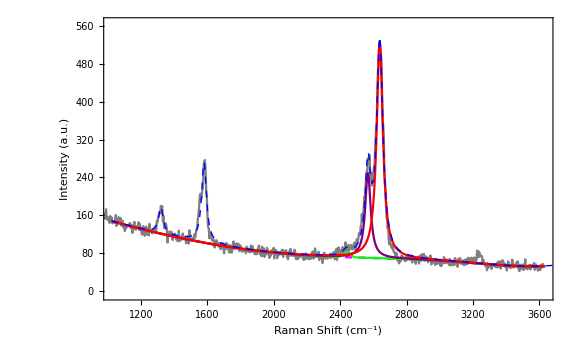

This is the data set, the data points used to fit the background (in red), and the plot of the background fit function (in magenta).

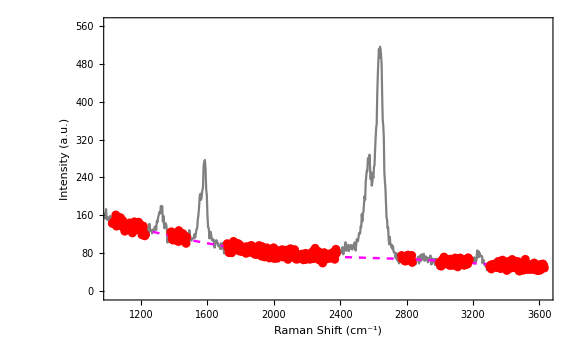

This is the best 2D peak fit, which is selected for the final plot. Blue is the 2D fit (combining however many lorentzians are used), magenta is the polynomial background.

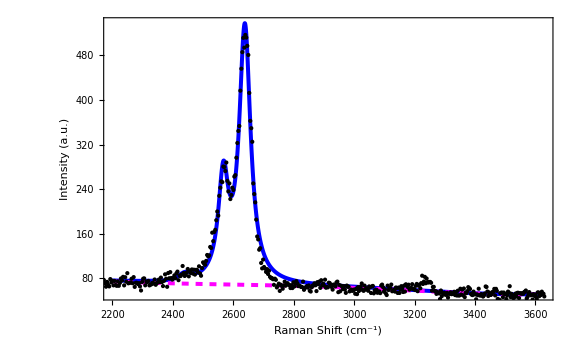

Single 2D peak fit with initial parameters: Blue is the combined total fit from equation fit2D1, green is the 2D peak lorentzian.

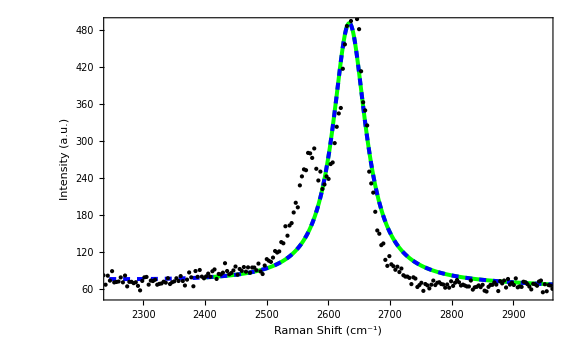

Double 2D peak fit: Blue is the combined total fit from equation fit2D2, red is the constrained gaussian and green is the 2D peak lorentzian.

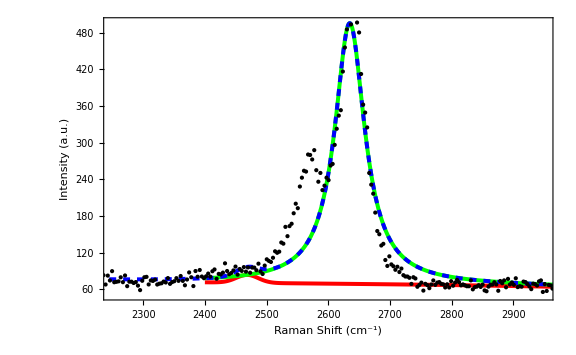

Triple 2D peak fit: Blue is the total fit from equation fit2D3, red is the constrained gaussian, purple is the strain peak lorentian and green is the 2D peak lorentzian.

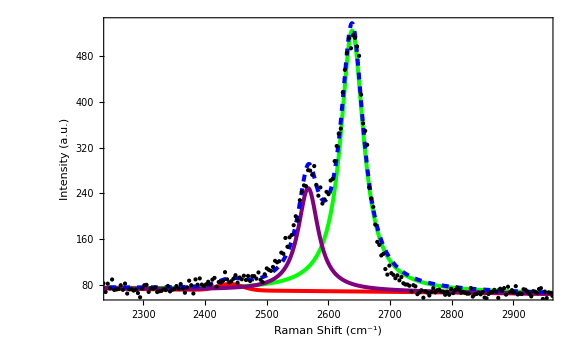

D peak fit: fitD

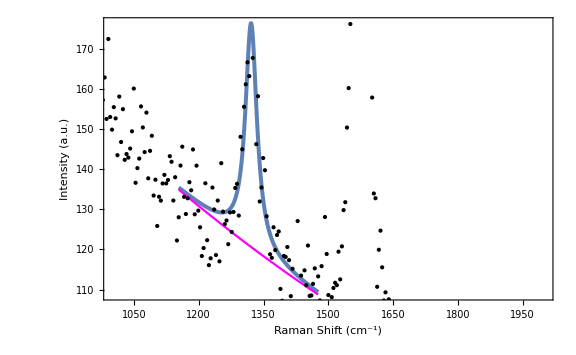

Gpeak fit. fitG

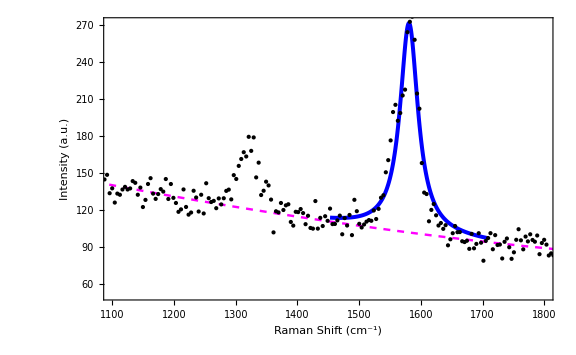

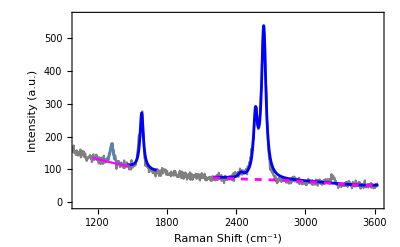

Check 11

ID is 55.8889

The fit results are

X | Y | Intensity(D) | Area(D) | FWHM(D) | Pos(D) | Intensity(G) | Area(G) | FWHM(G) | Pos(G) | Intensity(D+D') | Area(D+D') | FWHM(D+D') | Pos(D+D') | Intensity(Strained 2D) | Area(Strained 2D) | FWHM(Strained 2D) | Pos(Strained 2D) | Intensity(2D) | Area(2D) | FWHM(2D) | Pos(2D) | I2D)/I(G) | A(2D)/A(G)
21 | 26 | 55.8889 | 5675.9 | 32.3265 | 1321.34 | 169.851 | 18879.6 | 35.3814 | 1580.74 | 0.0262766 | 3.30201 | 40. | 2441.02 | 179.658 | 22576.5 | 40. | 2567.36 | 455.732 | 64791.5 | 45.2542 | 2638.58 | 2.68313 | 3.43182

Values assigned

```mathematica
(* Set the normalization constant for the distance vs number of plots for the 2D and 3D maps, i.e. if the step size is 0.5 micrometres then set m=0.5 and normalize the distance *)
m=1.;
(* Set the size of the steps for the histogram *)
bin=2000;

(* Distribute the above functions to all the parallel kernels *)
DistributeDefinitions[extractlocations,splitfilename,importdata,extractbackground,peakrangelist,constraintslist,selectpeakdata,initialparameterfunc,lorentzmodel,lorentzfunc,fit2Dfunc2,fit2Dfunc3,Dpeakfittingfunction2,exportfunction];

(*HERE WE EXTRACT THE CONTAINING FOLDER FILEPATHS, FILE NAMES, ETC. FROM THE FILEPATH*)
extractlocations[filepath]
(*EXTRACT THE NAME OF THE MAP AND THE NUMBER OF SPECTRA*)
splitfilename[filename]

(*DEFINE A RESULTS ARRAY*)
currentresult=Array[0&,{2,24}];  

(*HERE WE ENTER THE TITLES OF THE COLUMNS IN THE RESULTS FILE*)
currentresult[[1,1]]="X";
currentresult[[1,2]]="Y";

currentresult[[1,3]]="Intensity(D)";
currentresult[[1,4]]="Area(D)"; (*Area, D, fit[[4,1]]*)
currentresult[[1,5]]="FWHM(D)";
currentresult[[1,6]]="Pos(D)";(*Position, D, fit[[6,1]]*)

currentresult[[1,7]]="Intensity(G)";
currentresult[[1,8]]="Area(G)";(*Area, G, fit[[7,1]]*)
currentresult[[1,9]]="FWHM(G)";
currentresult[[1,10]]="Pos(G)";(*Position, G, fit[[9,1]]*)

currentresult[[1,11]]="Intensity(D+D')";
currentresult[[1,12]]="Area(D+D')";(*Area, 2D, fit[[10,1]]*)
currentresult[[1,13]]="FWHM(D+D')";
currentresult[[1,14]]="Pos(D+D')";(*Position, 2D, fit[[12,1]]*)

currentresult[[1,15]]="Intensity(Strained 2D)";
currentresult[[1,16]]="Area(Strained 2D)";(*Area, 2D, fit[[10,1]]*)
currentresult[[1,17]]="FWHM(Strained 2D)";
currentresult[[1,18]]="Pos(Strained 2D)";(*Position, 2D, fit[[12,1]]*)

currentresult[[1,19]]="Intensity(2D)";
currentresult[[1,20]]="Area(2D)";(*Area, 2D, fit[[10,1]]*)
currentresult[[1,21]]="FWHM(2D)";
currentresult[[1,22]]="Pos(2D)";(*Position, 2D, fit[[12,1]]*)

currentresult[[1,23]]="I2D)/I(G)";
currentresult[[1,24]]="A(2D)/A(G)";


Print["Check before"]
(*
Evaluate[Get[polynomialfitfilepath]]
*)
Needs["PolynomialFit`",polynomialfitfilepath]
Print["Check after"]

(*
(* CREATE DIRECTORIES TO EXPORT THE RESULTS AND SPECTRA TOO *)
resultsdir=CreateDirectory[dir<>ToString[mapname]<>";Results//"];
plotdir=CreateDirectory[dir<>ToString[mapname]<>";Spectra//"];
mapdir=CreateDirectory[dir<>ToString[mapname]<>";Fitted Maps//"];
*)

importdata[folderpath,mapname,X,Y];
Clear[peakDdata,peakGdata,peak2Ddata,
ADinit,wDinit,xDinit,AGinit,wGinit,xGinit,hGmax,hGmin,hGinit,A2Dinit,w2Dinit,x2Dinit,h2Dmax,h2Dmin,h2Dinit,
fit2D,fit2D1,fit2D2,fit2D3,fitG,fitD,
stddevfit2D,stddevfit2D1,stddevfit2D2,stddevfit2D3,
background,model2D1a,model2D2a,model2D2b,model2D3a,model2D3b,model2D3c,
fit2D1vals,fit2D1A1,fit2D1w1,fit2D1x1,fit2D1A2,fit2D1w2,fit2D1x2,fit2D1A3,fit2D1w3,fit2D1x3,
fit2D2vals,fit2D2A1,fit2D2w1,fit2D2x1,fit2D2A2,fit2D2w2,fit2D2x2,fit2D2A3,fit2D2w3,fit2D2x3,
fit2D3vals,fit2D3A1,fit2D3w1,fit2D3x1,fit2D3A2,fit2D3w2,fit2D3x2,fit2D3A3,fit2D3w3,fit2D3x3,
fit2Dvals,fit2DAa,fit2Dwa,fit2Dxa,fit2DAb,fit2Dwb,fit2Dxb,fit2DAc,fit2Dwc,fit2Dxc,
fitGvals,fitGA,fitGw,fitGx,
fitDvals,fitDA,fitDw,fitDx,
DfitOvals,DfitAO,DfitwO,DfitxO,
Dfitvals,DfitA,Dfitw,Dfitx,
model2D1a,model2D2a,model2D2b,model2D3a,model2D3b,model2D3c,model2D1,model2D2,model2D3,model2D,
ID,IG,IDDdash,Istrain,I2D,
background,backgroundDlist,
fitDlist,
Dbackgroundvariance,Dfitvariance,Dpeakvariance];

(* EXTRACT THE DATA FOR EACH PEAK SO IT CAN BE FIT SEPERATELY *)
{peakDdata,peakGdata,peak2Ddata}=selectpeakdata[fullmapdata,##]&@@@peakrangelist;
extractbackground[fullmapdata];

(* GET THE INITIAL PARAMETERS FOR THE PEAK FIT *)
initialparameters=initialparameterfunc/@{peakGdata,peak2Ddata,peakDdata};

(* ASSIGN THE CORRECT TITLES TO THE INITIAL PARAMETERS. *)
(* Note, the initialparametertitles list now gives the same contents as the initialparameters list when called but the titles it previously held have been assigned to the values. We clear it and define it again before calling the list so that it is reset to a list of titles each time the programme is run *)
initialparametertitles={{AGinit,wGinit,xGinit},{A2Dinit,w2Dinit,x2Dinit},{ADinit,wDinit,xDinit}};
Evaluate[initialparametertitles]=initialparameters;

(* NOW WE APPLY THE FITTING FUNCTIONS TO ALL THE PEAKS *)
background=PolynomialFit[backgrounddata,6];

Print["The background fit is"]
Print[background]
Print["The background value at x=250 is"]
Print[background[250]]

(* This fitting function uses constraints instead of initial parameter guesses but it stopped working after the Mathematica 10 upgrade so I have just commented it out and used the initial guess function.
Dfit=Dpeakfittingfunction2[background,peakDdata];//Quiet;
*)
Dfit=lorentzfunc[background,peakDdata,##]&@@initialparameters[[3]];//Quiet;
Gfit=lorentzfunc[background,peakGdata,##]&@@initialparameters[[1]];//Quiet;
(* 2D FITTING FUNCTIONS *)
fit2D1=lorentzfunc[background,peak2Ddata,##]&@@initialparameters[[2]];//Quiet;
fit2D2=fit2Dfunc2[background,peak2Ddata,##]&@@constraintslist[[1]];//Quiet;
fit2D3=fit2Dfunc3[background,peak2Ddata,##]&@@constraintslist[[2]];//Quiet;

(* ASSIGN NAMES TO ALL THE FIT PARAMETERS *)

(*  
{    0   ,    0   ,    0   ,    0   ,    0   ,    0   ,fit2D1A3,fit2D1w3,fit2D1x3},
{fit2D2A1,fit2D2w1,fit2D2x1,    0   ,    0   ,    0   ,fit2D2A3,fit2D2w3,fit2D2x3},
{fit2D3A1,fit2D3w1,fit2D3x1,fit2D3A2,fit2D3w2,fit2D3x2,fit2D3A3,fit2D3w3,fit2D3x3},
{ DfitA  , Dfitw  , Dfitx },
{ fitGA  , fitGw  , fitGx },
{ DfitAO , DfitwO , DfitxO},}
*)

(* ASSIGN NAMES TO ALL THE FIT PARAMETERS *)
fitparametertitles={
{fit2D1A3,fit2D1w3,fit2D1x3},
{fit2D2A1,fit2D2w1,fit2D2x1,fit2D2A3,fit2D2w3,fit2D2x3},
{fit2D3A1,fit2D3w1,fit2D3x1,fit2D3A2,fit2D3w2,fit2D3x2,fit2D3A3,fit2D3w3,fit2D3x3},
{DfitA,Dfitw,Dfitx},
{GfitA,Gfitw,Gfitx},
{DfitAO,DfitwO,DfitxO},
{GfitAO,GfitwO,GfitxO},
{fit2DAO,fit2DwO,fit2DxO}};

fit2D1A1=fit2D1w1=fit2D1x1=fit2D1A2=fit2D1w2=fit2D1x2=0;
fit2D2A2=fit2D2w2=fit2D2x2=0;
DfitAO=DfitwO=DfitxO=0;
GfitAO=GfitwO=GfitxO=0;
fit2DAOa=fit2DOwa=fit2DOxa=fit2DAOb=fit2DOwb=fit2DOxb=fit2DAOc=fit2DOwc=fit2DOxc=0;

fit2D1Parameters=fit2D1["ParameterTableEntries"];
fit2D2Parameters=fit2D2["ParameterTableEntries"];
fit2D3Parameters=fit2D3["ParameterTableEntries"];

Print[" fitDParameters=fitD[ParameterTableEntries] "]
DfitParameters=Dfit["ParameterTableEntries"]
Print[" fitGParameters=fitG[ParameterTableEntries] "]
fitGParameters=Gfit["ParameterTableEntries"]


Evaluate[fitparametertitles[[1]]]=fit2D1Parameters[[All,1]];//Quiet;
Evaluate[fitparametertitles[[2]]]=fit2D2Parameters[[All,1]];//Quiet;
Evaluate[fitparametertitles[[3]]]=fit2D3Parameters[[All,1]];//Quiet;


Evaluate[fitparametertitles[[4]]]=DfitParameters[[All,1]];//Quiet;
Evaluate[fitparametertitles[[5]]]=fitGParameters[[All,1]];//Quiet;

(* SELECT THE BEST FIT BY CHOOSING THE ONE WITH THE SMALLEST STANDARD DEVIATION, WITH AREA TESTING FUNCTION *)
(* If the area of any of the peaks in the fit is negative the if statement makes that std deviation equivalent to infinity so that it is disregarded as a candidate for the Best Fit *)

fit2D1vals={fit2D1A1,fit2D1w1,fit2D1x1,fit2D1A2,fit2D1w2,fit2D1x2,fit2D1A3,fit2D1w3,fit2D1x3};
fit2D2vals={fit2D2A1,fit2D2w1,fit2D2x1,fit2D2A2,fit2D2w2,fit2D2x2,fit2D2A3,fit2D2w3,fit2D2x3};
fit2D3vals={fit2D3A1,fit2D3w1,fit2D3x1,fit2D3A2,fit2D3w2,fit2D3x2,fit2D3A3,fit2D3w3,fit2D3x3};
fit2Dvals={fit2DAa,fit2Dwa,fit2Dxa,fit2DAb,fit2Dwb,fit2Dxb,fit2DAc,fit2Dwc,fit2Dxc};
fitGvals={fitGA,fitGw,fitGx};

Dfitvals={DfitA,Dfitw,Dfitx};
DfitOvals={DfitAO,DfitwO,DfitxO};
fitDvals={fitDA,fitDw,fitDx};

Gfitvals={GfitA,Gfitw,Gfitx};
GfitOvals={GfitAO,GfitwO,GfitxO};
fitGvals={fitGA,fitGw,fitGx};

fit2DOvals={fit2DAOa,fit2DOwa,fit2DOxa,fit2DAOb,fit2DOwb,fit2DOxb,fit2DAOc,fit2DOwc,fit2DOxc};


(* ----------------------------------  Test the 2D peak fit  ---------------------------------- *)
If[fit2D1A3>0,stddevfit2D1:=fit2D1["ANOVATableEntries"][[2,2]],stddevfit2D1:=Infinity];//Quiet;
If[fit2D2A1>0&&fit2D2A3>0,stddevfit2D2:=fit2D2["ANOVATableEntries"][[2,2]],stddevfit2D2:=Infinity];//Quiet;
If[fit2D3A1>0&&fit2D3A2>0&&fit2D3A3>0,stddevfit2D3:=fit2D3["ANOVATableEntries"][[2,2]],stddevfit2D3:=Infinity];//Quiet;
stddevfit2D=Min[stddevfit2D1,stddevfit2D2,stddevfit2D3];

fit2Dinit=Which[stddevfit2D==stddevfit2D1,fit2D1,stddevfit2D==stddevfit2D2,fit2D2,stddevfit2D==stddevfit2D3,fit2D3];//Quiet;
Evaluate[fit2Dinitvals]=Which[stddevfit2D==stddevfit2D1,fit2D1vals,stddevfit2D==stddevfit2D2,fit2D2vals,stddevfit2D==stddevfit2D3,fit2D3vals];//Quiet;
(* --------------------------------------------------------------------------------------------- *)



(* -----------------------------------  Test the D peak fit  ----------------------------------- *)
Print["Dfit is "]
Dfit
Print[" fitDO = 0 "]
DfitO=(background[#]+0*#)&

backgroundDlist=Table[{peakDdata[[x,1]],background[peakDdata[[x,1]]]},{x,1,Length[peakDdata]}];
fitDlist=Table[{x,Dfit[x]},{x,peakDdata[[1,1]],peakDdata[[-1,1]],1}];

Print[" The background fit to data variance is "]
Dbackgroundvariance=VarianceEquivalenceTest[{peakDdata[[All,2]],backgroundDlist[[All,2]]}]
Print[" The D peak fit to data variance is "]
Dfitvariance=VarianceEquivalenceTest[{peakDdata[[All,2]],fitDlist[[All,2]]}]
Print[" The Dpeakvariance is "]
Dpeakvariance=Max[Dbackgroundvariance,Dfitvariance]

Print[" fitD=Which[Dpeakvariance==Dbackgroundvariance,fitDO,Dpeakvariance==Dfitvariance,Dfit] "]
fitD=Which[Dpeakvariance==Dbackgroundvariance,DfitO,Dpeakvariance==Dfitvariance,Dfit]
Print[" Evaluate[fitDvals]=Which[Dpeakvariance==Dbackgroundvariance,Dfitvals,Dpeakvariance==Dfitvariance,fitDOvals] "]
Evaluate[fitDvals]=Which[Dpeakvariance==Dbackgroundvariance,DfitOvals,Dpeakvariance==Dfitvariance,Dfitvals]

Print["fitD is "]
fitD

Print["fitDvals are "]
fitDvals

(* --------------------------------------------------------------------------------------------- *)
(* -----------------------------------  Test the G peak fit  ----------------------------------- *)
(* --------------------------------------------------------------------------------------------- *)

Print["Gfit is "]
Gfit
Print[" fitGO is "]
GfitO=(background[#]+0*#)&

backgroundGlist=Table[{peakGdata[[x,1]],background[peakGdata[[x,1]]]},{x,1,Length[peakGdata]}];
fitGlist=Table[{x,Gfit[x]},{x,peakGdata[[1,1]],peakGdata[[-1,1]],0.5}];

Print[" The background fit to data variance is "]
Gbackgroundvariance=VarianceEquivalenceTest[{peakGdata[[All,2]],backgroundGlist[[All,2]]}]
Print[" The G peak fit to data variance is "]
Gfitvariance=VarianceEquivalenceTest[{peakGdata[[All,2]],fitGlist[[All,2]]}]
Print[" The Gpeakvariance is "]
Gpeakvariance=Max[Gbackgroundvariance,Gfitvariance]

Print[" fitG=Which[Gpeakvariance==Gbackgroundvariance,fitGO,Gpeakvariance==Gfitvariance,Gfit] "]
fitG=Which[Gpeakvariance==Gbackgroundvariance,GfitO,Gpeakvariance==Gfitvariance,Gfit]
Print["Evaluate[fitDvals]=Which[Gpeakvariance==Gbackgroundvariance,GfitOvals,Gpeakvariance==Gfitvariance,Gfitvals]"]
Evaluate[fitGvals]=Which[Gpeakvariance==Gbackgroundvariance,GfitOvals,Gpeakvariance==Gfitvariance,Gfitvals]

Print["fitG is "]
fitG

Print["fitGvals are "]
fitGvals

(* --------------------------------------------------------------------------------------------- *)
(* -----------------------------------  Test the 2D peak fit  ----------------------------------- *)
(* --------------------------------------------------------------------------------------------- *)

Print["2Dfitinit is "]
fit2Dinit
Print[" fit2DO is "]
fit2DO=(background[#]+0*#)&

background2Dlist=Table[{peak2Ddata[[x,1]],background[peak2Ddata[[x,1]]]},{x,1,Length[peak2Ddata]}];
fit2Dlist=Table[{x,fit2Dinit[x]},{x,peak2Ddata[[1,1]],peak2Ddata[[-1,1]],1}];

Print[" The background fit to data variance is "]
background2Dvariance=VarianceEquivalenceTest[{peak2Ddata[[All,2]],background2Dlist[[All,2]]}]
Print[" The D peak fit to data variance is "]
fit2Dvariance=VarianceEquivalenceTest[{peak2Ddata[[All,2]],fit2Dlist[[All,2]]}]
Print[" The Dpeakvariance is "]
peak2Dvariance=Max[background2Dvariance,fit2Dvariance]

Print[" fit2D=Which[2Dpeakvariance==2Dbackgroundvariance,fit2DO,2Dpeakvariance==2Dfitvariance,2Dfit] "]
fit2D=Which[peak2Dvariance==background2Dvariance,fit2DO,peak2Dvariance==fit2Dvariance,fit2Dinit]
Print[" Evaluate[fitDvals]=Which[Dpeakvariance==Dbackgroundvariance,Dfitvals,Dpeakvariance==Dfitvariance,fitDOvals] "]
Evaluate[fit2Dvals]=Which[peak2Dvariance==background2Dvariance,fit2DOvals,peak2Dvariance==fit2Dvariance,fit2Dinitvals]

Print["fit2D is "]
fit2D

Print["fitDvals are "]
fit2Dvals

(* --------------------------------------------------------------------------------------------- *)
(* --------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------- *)



(* NOTE: w is the half-width-half-maximum *)
Print[mapname,"_",X,"_",Y];
Print["D peak: A = ",fitDvals[[1]],", w = ",fitDvals[[2]],", pos = ",fitDvals[[3]],"."];
Print["G peak: A = ",fitGvals[[1]],", w = ",fitGvals[[2]],", pos = ",fitGvals[[3]],"."];
Print["D+Ddash: A = ",fit2Dvals[[1]],", w = ",fit2Dvals[[2]],", pos = ",fit2Dvals[[3]],"."];
Print["Strained 2D peak: A = ",fit2Dvals[[4]],", w = ",fit2Dvals[[5]],", pos = ",fit2Dvals[[6]],"."];
Print["2D peak: A = ",fit2Dvals[[7]],", w = ",fit2Dvals[[8]],", pos = ",fit2Dvals[[9]],"."];


(* CREATE MODELS FOR THE INDIVIDUAL FITS AND THEN USE AN 'IF' FUNCTION TO CHOOSE WHICH ONE TO USE *)
model2D1a=background[x]+lorentzmodel[fit2D1A3,fit2D1w3,fit2D1x3,x];
model2D2a=background[x]+gaussmodel[fit2D2A1,fit2D2w1,fit2D2x1,x];
model2D2b=background[x]+lorentzmodel[fit2D2A3,fit2D2w3,fit2D2x3,x];
model2D3a=background[x]+gaussmodel[fit2D3A1,fit2D3w1,fit2D3x1,x];
model2D3b=background[x]+lorentzmodel[fit2D3A2,fit2D3w2,fit2D3x2,x];
model2D3c=background[x]+lorentzmodel[fit2D3A3,fit2D3w3,fit2D3x3,x];


model2D1=Plot[model2D1a, {x,backgrounddata[[1,1]],backgrounddata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Red},AxesOrigin->{0,0},PlotRange->{{2200,backgrounddata[[-1,1]]},All},Epilog-> Map[Point,fullmapdata]];
model2D2=Plot[{model2D2a,model2D2b}, {x,backgrounddata[[1,1]],backgrounddata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Green,Red},AxesOrigin->{0,0},PlotRange->{{2200,backgrounddata[[-1,1]]},All},Epilog-> Map[Point,fullmapdata]];
model2D3=Plot[{model2D3a,model2D3b,model2D3c}, {x,backgrounddata[[1,1]],backgrounddata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Green,Purple,Red},AxesOrigin->{0,0},PlotRange->{{2200,backgrounddata[[-1,1]]},All},Epilog-> Map[Point,fullmapdata]];

model2D=Which[stddevfit2D==stddevfit2D1,model2D1,stddevfit2D==stddevfit2D2,model2D2,stddevfit2D==stddevfit2D3,model2D3];//Quiet;


(* PLOT THE FITTED PEAKS INDIVIDUALLY AND THE COMPLETE FIT *)

(* ----------------------------------------------------------------------------------------------------------- *)
(* ----------------------------------------------------------------------------------------------------------- *)
(* ----------------------------------------------------------------------------------------------------------- *)

(* Plot the complete spectrum with fits *)
backgroundplot=Plot[background[x],{x,backgrounddata[[1,1]],backgrounddata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},
PlotStyle->{Thickness[0.003],Dashed, Magenta},PlotRange->{{backgrounddata[[1,1]],backgrounddata[[-1,1]]},All}];

dataplot=ListLinePlot[fullmapdata,Frame->True ,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->Gray,PlotRange->{{backgrounddata[[1,1]],backgrounddata[[-1,1]]},{Min[fullmapdata[[All,2]]]-50,Max[fullmapdata[[All,2]]+50]}},AxesOrigin->{0,0},ImageSize->{Automatic,800}];

Print[" Check   5"]
fitplot=Plot[{fit2D[x]+fitG[x]+fitD [x]-(2 background[x])}, {x,0,5000},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thick,Dashed,Blue},PlotRange->{{backgrounddata[[1,1]],backgrounddata[[-1,1]]},All}];

(* plotxy= *)
Print[Style["This is the complete fit which is exported.",Large]]
Show[dataplot,backgroundplot,model2D,fitplot,ImageSize->Large,LabelStyle->(FontSize->20)]

backgrounddataplot=ListPlot[backgrounddata,Frame->True ,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.002],Red},PlotRange->All];

Print[Style["This is the data set, the data points used to fit the background (in red), and the plot of the background fit function (in magenta).",Large]]
Show[dataplot,backgroundplot,backgrounddataplot,ImageSize->Large,LabelStyle->(FontSize-> 20)]

(* PLOT THE FITTED PEAKS INDIVIDUALLY AND THE COMPLETE FIT *)
Print[Style["This is the best 2D peak fit, which is selected for the final plot. Blue is the 2D fit (combining however many lorentzians are used), magenta is the polynomial background.",Large]]
bestfit=
Plot[{fit2D[x],background[x]}, {x,2200,backgrounddata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Dashed,Magenta}},AxesOrigin->{0,0},PlotRange->{{2200,backgrounddata[[-1,1]]},All},Epilog-> Map[Point,fullmapdata]];
Show[bestfit,ImageSize->Large,LabelStyle->(FontSize-> 20)]

Print[Style["Single 2D peak fit with initial parameters: Blue is the combined total fit from equation fit2D1, green is the 2D peak lorentzian.",Large]]
fit2D1plot=Plot[{fit2D1[x]}, {x,2200,3050},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005],Dashed,Blue},AxesOrigin->{0,0},PlotRange->{{2200,3000},All},Epilog-> Map[Point,fullmapdata]];
modelplot2D1a=Plot[model2D1a, {x,2400,backgrounddata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005],Green},AxesOrigin->{0,0},PlotRange->{{2250,2950},All},Epilog-> Map[Point,fullmapdata]];
Show[modelplot2D1a,fit2D1plot,ImageSize->Large,LabelStyle->(FontSize-> 20)]


Print[Style["Double 2D peak fit: Blue is the combined total fit from equation fit2D2, red is the constrained gaussian and green is the 2D peak lorentzian.",Large]]
fit2D2plot=Plot[fit2D2[x], {x,2200,backgrounddata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005],Dashed,Blue},AxesOrigin->{0,0},PlotRange->{{2200,3000},All},Epilog-> Map[Point,fullmapdata]];
modelplot2D2a=Plot[model2D2a, {x,2400,backgrounddata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005],Red},AxesOrigin->{0,0},
PlotRange->{{2250,2950},All},Epilog-> Map[Point,fullmapdata]];
modelplot2D2b=Plot[model2D2b, {x,2400,backgrounddata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005],Green},AxesOrigin->{0,0},PlotRange->{{2200,3000},All},Epilog-> Map[Point,fullmapdata]];
Show[modelplot2D2a,modelplot2D2b,fit2D2plot,ImageSize->Large,LabelStyle->(FontSize-> 20)]


Print[Style["Triple 2D peak fit: Blue is the total fit from equation fit2D3, red is the constrained gaussian, purple is the strain peak lorentian and green is the 2D peak lorentzian.",Large]]
fit2D3plot=Plot[fit2D3[x], {x,2200,3000},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005],Dashed,Blue},AxesOrigin->{0,0},PlotRange->{{2250,2950},All},Epilog-> Map[Point,fullmapdata]];
modelplot2D3a=Plot[model2D3a, {x,2200,3000},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005],Red},AxesOrigin->{0,0},PlotRange->{{2250,2950},All},Epilog-> Map[Point,fullmapdata]];

modelplot2D3b=Plot[model2D3b, {x,2200,3000},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005],Purple},AxesOrigin->{0,0},PlotRange->{{2250,2950},All},Epilog-> Map[Point,fullmapdata]];

modelplot2D3c=Plot[model2D3c, {x,2200,3000},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005],Green},AxesOrigin->{0,0},PlotRange->{{2250,2950},All},
Epilog-> Map[Point,fullmapdata]];
Show[modelplot2D3c,modelplot2D3a,modelplot2D3b,fit2D3plot,ImageSize->Large,LabelStyle->(FontSize-> 20)]


Print[Style["D peak fit: fitD",Large]]
peakplotD=Plot[{fitD[x],background[x]},{x,peakDdata[[1,1]],peakDdata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005],{Blue,Magenta}},AxesOrigin->{0,0},PlotRange->{{1000,2000},All},Epilog-> Map[Point,fullmapdata]];
Show[peakplotD,ImageSize->Large,LabelStyle->(FontSize-> 20)]

Print[Style["Gpeak fit. fitG",Large]]
peakplotG=Plot[fitG[x],{x,peakGdata[[1,1]],peakGdata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005],Blue},AxesOrigin->{0,0},PlotRange->{{1100,1800},All},Epilog-> Map[Point,fullmapdata]];
Show[peakplotG,backgroundplot,ImageSize->Large,LabelStyle->(FontSize-> 20)]

fitplot=Plot[{fit2D[x]+fitG[x]+fitD[x]-(2 background[x])}, {x,backgrounddata[[1,1]],backgrounddata[[-1,1]]},Frame->True,FrameLabel->{"Raman Shift (cm^-1)","Intensity (a.u.)"},PlotStyle->{Thickness[0.003],AbsoluteDashing[{12,6}],Blue},AxesOrigin->{0,0},PlotRange->{{backgrounddata[[1,1]],backgrounddata[[-1,1]]},All}];

Show[dataplot,peakplotG,peakplotD,bestfit,ImageSize->{Automatic,400},LabelStyle->(FontSize-> 20)]

(* Export an image of the spectrum and plot*)
(*
Export[FileNameJoin[{plotdir,StringJoin["Spectrum;",ToString[mapname],"_",ToString[X],"_",ToString[Y],".png"]}],plotxy,"PNG"];
*)

(*CALCULATE THE INTENSITIES OF THE PEAKS*)
(* Height, hD=AD/(Pi*FWHM) -- (If A≥0,results=h, If:A<0,results=1)*)
ID=Which[(fitDvals[[1]])>0,fitDvals[[1]]/(Pi Abs[fitDvals[[2]]*2]),(fitDvals[[1]])≤0,1];
IG=Which[(fitGvals[[1]])>0,fitGvals[[1]]/(Pi (Abs[fitGvals[[2]]*2])),(fitGvals[[1]])≤0,1];(* Height, hD=AD/(Pi*FWHM) *)
IDDdash=Which[(fit2Dvals[[1]])>0,fit2Dvals[[1]]/(Pi (Abs[fit2Dvals[[2]]*2])),(fit2Dvals[[1]])≤0,1];
Istrain=Which[(fit2Dvals[[4]])>0,fit2Dvals[[4]]/(Pi (Abs[fit2Dvals[[5]]*2])),(fit2Dvals[[4]])≤0,1];
I2D=Which[(fit2Dvals[[7]])>0,fit2Dvals[[7]]/(Pi (Abs[fit2Dvals[[8]]*2])),(fit2Dvals[[7]])≤0,1];


Print["Check 11"];     (* !!!!!!!!!!!!!!!! *)

currentresult[[2,1]]=X; (* !!!!!!!!!!!!!!!! *)
currentresult[[2,2]]=Y; (* !!!!!!!!!!!!!!!! *)

Print["ID is ",ID];
currentresult[[2,3]]=ID; (* !!!!!!!!!!!!!!!! *)
currentresult[[2,4]]=fitDvals[[1]]; (* Area *)
currentresult[[2,5]]=Abs[fitDvals[[2]]*2];(* FWHM *)
currentresult[[2,6]]=fitDvals[[3]];(* x position *)

currentresult[[2,7]]=IG;
currentresult[[2,8]]=fitGvals[[1]];(* Area *)
currentresult[[2,9]]=Abs[fitGvals[[2]]*2];(* FWHM *)
currentresult[[2,10]]=fitGvals[[3]];(* x position *)

currentresult[[2,11]]=IDDdash;
currentresult[[2,12]]=fit2Dvals[[1]];(* Area *)
currentresult[[2,13]]=Abs[fit2Dvals[[2]]*2];(* FWHM *)
currentresult[[2,14]]=fit2Dvals[[3]];(* x position *)

currentresult[[2,15]]=Istrain;
currentresult[[2,16]]=fit2Dvals[[4]];(* Area *)
currentresult[[2,17]]=Abs[fit2Dvals[[5]]*2];(* FWHM *)
currentresult[[2,18]]=fit2Dvals[[6]];(* x position *)

currentresult[[2,19]]=I2D;
currentresult[[2,20]]=fit2Dvals[[7]];(* Area *)
currentresult[[2,21]]=Abs[fit2Dvals[[8]]*2];(* FWHM *)
currentresult[[2,22]]=fit2Dvals[[9]];(* x position *)

currentresult[[2,23]]=I2D/IG;
currentresult[[2,24]]=(fit2Dvals[[7]])/(fitGvals[[1]]);

Print["The fit results are "];
Print[currentresult//TableForm];
(*
Export[FileNameJoin[{resultsdir,StringJoin[ToString[mapname],"_",ToString[X],"_",ToString[Y],".txt"]}],currentresult,"TSV"];
*)
Print["Values assigned"];

(* !!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!! *)
(* The main programme is finished and the fit data exported as seperate files *)
(* Now we import each file and add it to a complete array of all the data     *)
(* !!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!! *)
```